# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-03

```mathematica
states=Union[seqData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Arizona→{{2021-12-20,225},{2021-12-21,275},{2021-12-22,328},{2021-12-23,231},{2021-12-24,32},{2021-12-25,19},{2021-12-26,64},{2021-12-27,183},{2021-12-28,330},{2021-12-29,75},{2021-12-30,169},{2021-12-31,75},{2022-01-01,53},{2022-01-02,241},{2022-01-03,217}},California→{{2021-12-20,2493},{2021-12-21,3804},{2021-12-22,4694},{2021-12-23,3499},{2021-12-24,413},{2021-12-25,72},{2021-12-26,743},{2021-12-27,3108},{2021-12-28,720},{2021-12-29,169},{2021-12-30,541},{2021-12-31,456},{2022-01-01,39},{2022-01-02,774},{2022-01-03,137}},Colorado→{{2021-12-20,883},{2021-12-21,635},{2021-12-22,713},{2021-12-23,688},{2021-12-24,366},{2021-12-25,365},{2021-12-26,244},{2021-12-27,318},{2021-12-28,319},{2021-12-29,616},{2021-12-30,155},{2021-12-31,89},{2022-01-01,18},{2022-01-02,9},{2022-01-03,219}},Connecticut→{{2021-12-20,199},{2021-12-21,204},{2021-12-22,251},{2021-12-23,259},{2021-12-24,121},{2021-12-25,8},{2021-12-26,143},{2021-12-27,248},{2021-12-28,179},{2021-12-29,208},{2021-12-30,52},{2021-12-31,22},{2022-01-01,2},{2022-01-02,69},{2022-01-03,120}},Florida→{{2021-12-20,323},{2021-12-21,476},{2021-12-22,521},{2021-12-23,248},{2021-12-24,13},{2021-12-25,14},{2021-12-26,498},{2021-12-27,324},{2021-12-28,226},{2021-12-29,172},{2021-12-30,140},{2021-12-31,4},{2022-01-01,15},{2022-01-02,111},{2022-01-03,13}},Georgia→{{2021-12-20,286},{2021-12-21,243},{2021-12-22,233},{2021-12-23,125},{2021-12-24,19},{2021-12-25,9},{2021-12-26,217},{2021-12-27,236},{2021-12-28,160},{2021-12-29,125},{2021-12-30,65},{2021-12-31,3},{2022-01-01,0},{2022-01-02,38},{2022-01-03,0}},Illinois→{{2021-12-20,294},{2021-12-21,283},{2021-12-22,433},{2021-12-23,224},{2021-12-24,29},{2021-12-25,15},{2021-12-26,240},{2021-12-27,241},{2021-12-28,127},{2021-12-29,45},{2021-12-30,65},{2021-12-31,32},{2022-01-01,18},{2022-01-02,44},{2022-01-03,31}},Indiana→{{2021-12-20,84},{2021-12-21,74},{2021-12-22,91},{2021-12-23,167},{2021-12-24,0},{2021-12-25,0},{2021-12-26,48},{2021-12-27,109},{2021-12-28,51},{2021-12-29,40},{2021-12-30,9},{2021-12-31,2},{2022-01-01,0},{2022-01-02,21},{2022-01-03,22}},Louisiana→{{2021-12-20,113},{2021-12-21,111},{2021-12-22,86},{2021-12-23,84},{2021-12-24,39},{2021-12-25,3},{2021-12-26,40},{2021-12-27,71},{2021-12-28,207},{2021-12-29,53},{2021-12-30,54},{2021-12-31,35},{2022-01-01,0},{2022-01-02,20},{2022-01-03,8}},Maryland→{{2021-12-20,199},{2021-12-21,413},{2021-12-22,191},{2021-12-23,113},{2021-12-24,68},{2021-12-25,90},{2021-12-26,98},{2021-12-27,108},{2021-12-28,109},{2021-12-29,230},{2021-12-30,68},{2021-12-31,63},{2022-01-01,58},{2022-01-02,77},{2022-01-03,53}},Massachusetts→{{2021-12-20,793},{2021-12-21,1094},{2021-12-22,623},{2021-12-23,449},{2021-12-24,28},{2021-12-25,6},{2021-12-26,698},{2021-12-27,1207},{2021-12-28,667},{2021-12-29,1386},{2021-12-30,1205},{2021-12-31,168},{2022-01-01,170},{2022-01-02,940},{2022-01-03,1272}},Michigan→{{2021-12-20,146},{2021-12-21,144},{2021-12-22,150},{2021-12-23,117},{2021-12-24,8},{2021-12-25,9},{2021-12-26,76},{2021-12-27,160},{2021-12-28,78},{2021-12-29,44},{2021-12-30,40},{2021-12-31,17},{2022-01-01,1},{2022-01-02,23},{2022-01-03,6}},Minnesota→{{2021-12-20,71},{2021-12-21,72},{2021-12-22,59},{2021-12-23,64},{2021-12-24,28},{2021-12-25,24},{2021-12-26,30},{2021-12-27,21},{2021-12-28,74},{2021-12-29,562},{2021-12-30,17},{2021-12-31,14},{2022-01-01,7},{2022-01-02,8},{2022-01-03,32}},Nebraska→{{2021-12-20,74},{2021-12-21,37},{2021-12-22,15},{2021-12-23,10},{2021-12-24,20},{2021-12-25,17},{2021-12-26,37},{2021-12-27,119},{2021-12-28,143},{2021-12-29,103},{2021-12-30,18},{2021-12-31,4},{2022-01-01,4},{2022-01-02,17},{2022-01-03,50}},Nevada→{{2021-12-20,88},{2021-12-21,113},{2021-12-22,143},{2021-12-23,31},{2021-12-24,10},{2021-12-25,8},{2021-12-26,85},{2021-12-27,205},{2021-12-28,24},{2021-12-29,5},{2021-12-30,10},{2021-12-31,19},{2022-01-01,0},{2022-01-02,1},{2022-01-03,4}},New Jersey→{{2021-12-20,141},{2021-12-21,681},{2021-12-22,967},{2021-12-23,289},{2021-12-24,22},{2021-12-25,4},{2021-12-26,92},{2021-12-27,109},{2021-12-28,36},{2021-12-29,67},{2021-12-30,36},{2021-12-31,36},{2022-01-01,4},{2022-01-02,4},{2022-01-03,4}},New Mexico→{{2021-12-20,31},{2021-12-21,43},{2021-12-22,47},{2021-12-23,34},{2021-12-24,14},{2021-12-25,5},{2021-12-26,29},{2021-12-27,21},{2021-12-28,18},{2021-12-29,37},{2021-12-30,22},{2021-12-31,13},{2022-01-01,20},{2022-01-02,31},{2022-01-03,33}},New York→{{2021-12-20,743},{2021-12-21,581},{2021-12-22,716},{2021-12-23,743},{2021-12-24,202},{2021-12-25,83},{2021-12-26,65},{2021-12-27,339},{2021-12-28,247},{2021-12-29,172},{2021-12-30,80},{2021-12-31,76},{2022-01-01,15},{2022-01-02,10},{2022-01-03,54}},North Carolina→{{2021-12-20,181},{2021-12-21,233},{2021-12-22,266},{2021-12-23,167},{2021-12-24,70},{2021-12-25,36},{2021-12-26,109},{2021-12-27,318},{2021-12-28,175},{2021-12-29,308},{2021-12-30,222},{2021-12-31,52},{2022-01-01,49},{2022-01-02,55},{2022-01-03,153}},North Dakota→{{2021-12-20,37},{2021-12-21,94},{2021-12-22,58},{2021-12-23,118},{2021-12-24,21},{2021-12-25,9},{2021-12-26,20},{2021-12-27,57},{2021-12-28,125},{2021-12-29,34},{2021-12-30,72},{2021-12-31,18},{2022-01-01,1},{2022-01-02,34},{2022-01-03,70}},Ohio→{{2021-12-20,264},{2021-12-21,273},{2021-12-22,246},{2021-12-23,103},{2021-12-24,2},{2021-12-25,1},{2021-12-26,74},{2021-12-27,89},{2021-12-28,17},{2021-12-29,2},{2021-12-30,87},{2021-12-31,0},{2022-01-01,0},{2022-01-02,1},{2022-01-03,83}},Oregon→{{2021-12-20,44},{2021-12-21,91},{2021-12-22,61},{2021-12-23,68},{2021-12-24,29},{2021-12-25,12},{2021-12-26,45},{2021-12-27,51},{2021-12-28,75},{2021-12-29,72},{2021-12-30,33},{2021-12-31,16},{2022-01-01,7},{2022-01-02,3},{2022-01-03,36}},Pennsylvania→{{2021-12-20,96},{2021-12-21,110},{2021-12-22,180},{2021-12-23,179},{2021-12-24,27},{2021-12-25,0},{2021-12-26,44},{2021-12-27,52},{2021-12-28,63},{2021-12-29,66},{2021-12-30,47},{2021-12-31,50},{2022-01-01,0},{2022-01-02,19},{2022-01-03,0}},Tennessee→{{2021-12-20,81},{2021-12-21,122},{2021-12-22,75},{2021-12-23,120},{2021-12-24,10},{2021-12-25,8},{2021-12-26,42},{2021-12-27,181},{2021-12-28,57},{2021-12-29,29},{2021-12-30,37},{2021-12-31,2},{2022-01-01,1},{2022-01-02,0},{2022-01-03,36}},Texas→{{2021-12-20,610},{2021-12-21,640},{2021-12-22,715},{2021-12-23,376},{2021-12-24,30},{2021-12-25,6},{2021-12-26,286},{2021-12-27,477},{2021-12-28,651},{2021-12-29,52},{2021-12-30,106},{2021-12-31,17},{2022-01-01,1},{2022-01-02,28},{2022-01-03,2}},Utah→{{2021-12-20,155},{2021-12-21,106},{2021-12-22,117},{2021-12-23,74},{2021-12-24,0},{2021-12-25,0},{2021-12-26,27},{2021-12-27,251},{2021-12-28,244},{2021-12-29,253},{2021-12-30,245},{2021-12-31,3},{2022-01-01,4},{2022-01-02,35},{2022-01-03,403}},Vermont→{{2021-12-20,10},{2021-12-21,7},{2021-12-22,4},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0},{2021-12-26,37},{2021-12-27,60},{2021-12-28,7},{2021-12-29,26},{2021-12-30,4},{2021-12-31,1},{2022-01-01,0},{2022-01-02,1},{2022-01-03,1}},Virginia→{{2021-12-20,31},{2021-12-21,142},{2021-12-22,111},{2021-12-23,40},{2021-12-24,1},{2021-12-25,1},{2021-12-26,19},{2021-12-27,21},{2021-12-28,24},{2021-12-29,198},{2021-12-30,39},{2021-12-31,0},{2022-01-01,0},{2022-01-02,3},{2022-01-03,1}},Washington→{{2021-12-20,232},{2021-12-21,276},{2021-12-22,179},{2021-12-23,93},{2021-12-24,254},{2021-12-25,7},{2021-12-26,94},{2021-12-27,262},{2021-12-28,398},{2021-12-29,226},{2021-12-30,150},{2021-12-31,47},{2022-01-01,2},{2022-01-02,109},{2022-01-03,105}},Wisconsin→{{2021-12-20,226},{2021-12-21,210},{2021-12-22,266},{2021-12-23,209},{2021-12-24,70},{2021-12-25,39},{2021-12-26,143},{2021-12-27,248},{2021-12-28,85},{2021-12-29,15},{2021-12-30,193},{2021-12-31,87},{2022-01-01,0},{2022-01-02,22},{2022-01-03,68}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

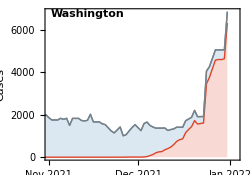

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

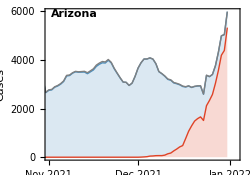
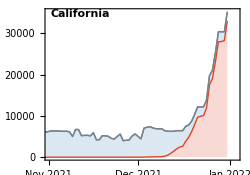
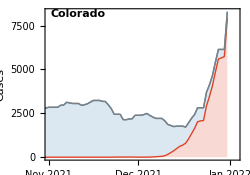
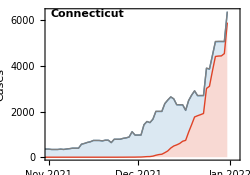
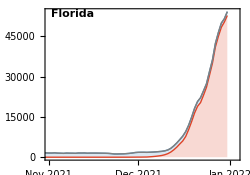
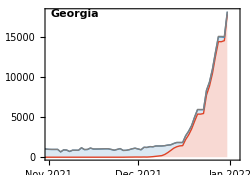
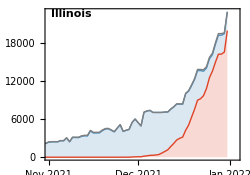
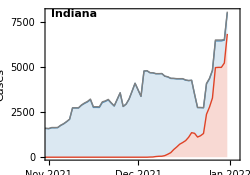
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png